```mathematica
从P倒推需要的Mdot
假设现在源处于spin equilibrium，又现在的周期P推出此时的Mdot，并由此倒推初始盘的质量和回落盘形成时间;
P1=1.427579,Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403,Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316,Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042,Pdot4=-4.7*^-9;MJD4=56851.5;
MJD in units of day;
```

```mathematica
case1,取Mdot为常数
```

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.39*10^18*m;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

P1=1.427579;
MJD1=52690.9;

Mdot=5*10^18;

B=10^15;
mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);


P=P1;
t=MJD1*24*3600.;
MJD4=56851.5*24*3600.;

dataP=Table[
n;
torque=Mdot*(G*M*Rin)^(1/2);
Pdot=-(torque*P^2.)/(2.*Pi*10^45.);
dt=If[t<MJD4,Min[10^-3*P/Abs[Pdot],10^-3*t],0];
t=t+dt;
P=P+Pdot*dt;
(*t=t/(24*3600.);*)
{t,P},
{n,1,1000}];
```

```mathematica
MJD4=56851.5;
MJD1*24*3600.
MJD4*24*3600.
```

4.55249×10^9

4.91197×10^9

```mathematica
t
P
```

4.9167×10^9

1.37458

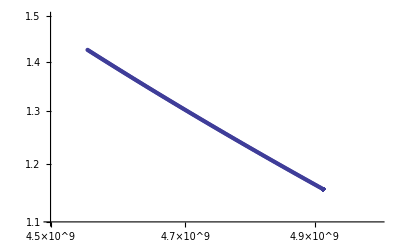

```mathematica
ListLogLogPlot[dataP,PlotRange->{{4.5*10^9,5*10^9},{1.1,1.5}}]
```

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;
m=1.4;
MdotEdd=1.39*10^18*m;(*Eddington accretion rate*)
M=m*Msun;
Irot=10^45;
xi=0.5;

P1=1.427579;Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
P=List[P1,P2,P3,P4];
Pdot=List[Pdot1,Pdot2,Pdot3,Pdot4];
torque1=-2*Pi*Irot*Pdot/P^2

B={B1,B2,B3,B4};
Mdot={Mdot1,Mdot2,Mdot3,Mdot4};
mu=0.5*B*R^3;
Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);
torque2=Mdot*(G*M*Rin)^(1/2)

Table[i;Solve[torque2[[i]]==torque1[[i]],{B[[i]],Mdot[[i]]}],{i,1,4}]
(*Solve[torque2==torque1,{B,Mdot}]*)

(*MJD=List[MJD1,MJD2,MJD3,MJD4];
PandMJD=List[MJD,P]//Transpose;
ListLinePlot[PandMJD[[2;;4]]]*)
```

{2.95972×10^37,2.52554×10^37,2.42878×10^37,2.28817×10^37}

{1.39301×10^16 (B1^4/Mdot1^2)^(1/14) Mdot1,1.39301×10^16 (B2^4/Mdot2^2)^(1/14) Mdot2,1.39301×10^16 (B3^4/Mdot3^2)^(1/14) Mdot3,1.39301×10^16 (B4^4/Mdot4^2)^(1/14) Mdot4}

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve :: svars will be suppressed during this calculation.

{{{Mdot1→-(7.61811×10^24)/B1^(1/3)},{Mdot1→-(0.+7.61811×10^24 ⅈ)/B1^(1/3)},{Mdot1→(0.+7.61811×10^24 ⅈ)/B1^(1/3)},{Mdot1→(7.61811×10^24)/B1^(1/3)}},{{Mdot2→-(6.33094×10^24)/B2^(1/3)},{Mdot2→-(0.+6.33094×10^24 ⅈ)/B2^(1/3)},{Mdot2→(0.+6.33094×10^24 ⅈ)/B2^(1/3)},{Mdot2→(6.33094×10^24)/B2^(1/3)}},{{Mdot3→-(6.04886×10^24)/B3^(1/3)},{Mdot3→-(0.+6.04886×10^24 ⅈ)/B3^(1/3)},{Mdot3→(0.+6.04886×10^24 ⅈ)/B3^(1/3)},{Mdot3→(6.04886×10^24)/B3^(1/3)}},{{Mdot4→-(5.64233×10^24)/B4^(1/3)},{Mdot4→-(0.+5.64233×10^24 ⅈ)/B4^(1/3)},{Mdot4→(0.+5.64233×10^24 ⅈ)/B4^(1/3)},{Mdot4→(5.64233×10^24)/B4^(1/3)}}}

```mathematica
{Mdot1->(7.618111583662568*^24)/B1^(1/3)};
{Mdot2->(6.330941226343839*^24)/B2^(1/3)};
{Mdot3->(6.048860474336591*^24)/B3^(1/3)};
{Mdot4->(5.642330295355947*^24)/B4^(1/3)};
```

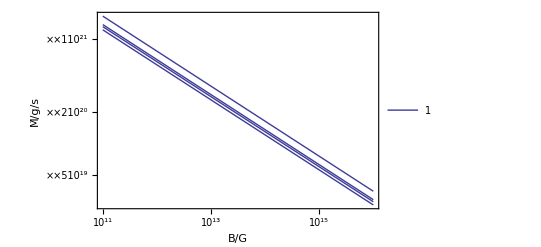

```mathematica
Clear["`*"]
k={7.61811,6.33094,6.04886,5.64233};
LogLogPlot[{Mdot=k*10^24/B^(1/3)},{B,10^11,10^16},Frame->True,FrameLabel->{"B/G","Ṁ/g/s"},PlotLegends->{"1","2","3","4"}]
```

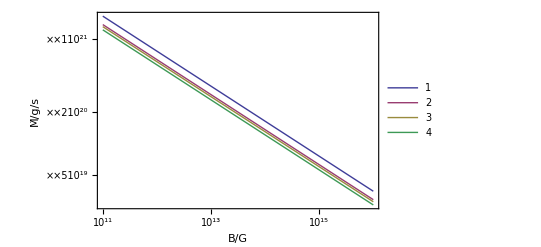

```mathematica
Clear["`*"]
k1=7.61811;k2=6.33094;k3=6.04886;k4=5.64233;
Mdot1=k1*10^24/B^(1/3);
Mdot2=k2*10^24/B^(1/3);
Mdot3=k3*10^24/B^(1/3);
Mdot4=k4*10^24/B^(1/3);
LogLogPlot[{Mdot1,Mdot2,Mdot3,Mdot4},{B,10^11,10^16},Frame->True,FrameLabel->{"B/G","Ṁ/g/s"},PlotLegends->{"1","2","3","4"}]
```

```mathematica
Clear["`*"]
B=10^15;
k1=7.61811;k2=6.33094;k3=6.04886;k4=5.64233;
Mdot1=k1*10^24/B^(1/3)
Mdot2=k2*10^24/B^(1/3)
Mdot3=k3*10^24/B^(1/3)
Mdot4=k4*10^24/B^(1/3)
```

7.61811×10^19

6.33094×10^19

6.04886×10^19

5.64233×10^19

```mathematica
P1=1.427579;Pdot1=-9.6*^-9;MJD1=52690.9;
P2=1.137403;Pdot2=-5.2*^-9;MJD2=56848.0;
P3=1.137316;Pdot3=-5.0*^-9;MJD3=56848.2;
P4=1.136042;Pdot4=-4.7*^-9;MJD4=56851.5;
```

```mathematica
Clear["`*"]
(*Mdot in units of 10^19*)
data={{690.9,7.61811},{4848.0,6.33094},{4848.2,6.04886},{4851.5,5.64233}};
Mdot=Mdot0*(t/t0)^-alpha;
(*alpha=1.14286;*)
(*-1.35714<=alpha≤-1.14286;*)
fit=FindFit[data,{Mdot,{1.14286<=alpha≤1.35714}},{Mdot0,t0,alpha},t]
(*{10^15<=Mdot0≤10^25,1<=t0≤10^8,-1.35714<=alpha≤-1.14286}*)
```

{Mdot0→89.0298,t0→95.1736,alpha→1.14286}

```mathematica
Clear["`*"]
(*Mdot in units of 10^19*)
data={{2690.9,7.61811},{6848.0,6.33094},{6848.2,6.04886},{6851.5,5.64233}};
Mdot=Mdot0*(t/t0)^-alpha;
(*alpha=1.14286;*)
(*-1.35714<=alpha≤-1.14286;*)
fit=FindFit[data,{Mdot,{1.14286<=alpha≤1.35714}},{Mdot0,t0,alpha},t]
(*{10^15<=Mdot0≤10^25,1<=t0≤10^8,-1.35714<=alpha≤-1.14286}*)
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.43248×10^-11, 0.0000138928, 7.27337×10^-12}, is returned.

{Mdot0→192.514,t0→205.804,alpha→1.14286}

```mathematica
Clear["`*"]
(*Mdot in units of 10^19*)
data={{90.9,7.61811},{4248.0,6.33094},{4248.2,6.04886},{4251.5,5.64233}};
Mdot=Mdot0*(t/t0)^-alpha;
(*alpha=1.14286;*)
(*-1.35714<=alpha≤-1.14286;*)
fit=FindFit[data,{Mdot,{1.14286<=alpha≤1.35714}},{Mdot0,t0,alpha},t]
(*{10^15<=Mdot0≤10^25,1<=t0≤10^8,-1.35714<=alpha≤-1.14286}*)
```

{Mdot0→27.9523,t0→29.8769,alpha→1.14286}

```mathematica
so alpha maybe euqals -8/7;
```

```mathematica
Mdot=Mdot0*(t/t0)^-alpha
```

```mathematica
Clear["`*"]
G=6.67*10^-8;
Msun=2*10^33;
m=1.4;
M=m*Msun;
R=10^6;
MdotEdd=1.39*10^18*m;

xi=0.5;


P1=1.427579;Pdot1=-9.6*^-9;
P2=1.137403;Pdot2=-5.2*^-9;
P3=1.137316;Pdot3=-5.0*^-9;
P4=1.136042;Pdot4=-4.7*^-9;
(*P=P4;
Pdot=Pdot4;*)

mu=0.5*B*R^3;

(*Rin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);
Rco=((G*M*P^2)/(4*Pi^2))^(1/3);*)


Mdoteq1=(51.51156* mu^2*(G*M*P1^2)^(1/3)*xi^(7/2))/(G^2*M^2*P1^3);
Mdoteq2=(51.51156* mu^2*(G*M*P2^2)^(1/3)*xi^(7/2))/(G^2*M^2*P2^3);
Mdoteq3=(51.51156* mu^2*(G*M*P3^2)^(1/3)*xi^(7/2))/(G^2*M^2*P3^3);
Mdoteq4=(51.51156* mu^2*(G*M*P4^2)^(1/3)*xi^(7/2))/(G^2*M^2*P4^3);
(*mdot=(51.51156* mu^2*(G*M*P^2)^(1/3)*xi^(7/2))/(G^2*M^2*P^3*MdotEdd);*)
MdotN1=((-2*Pi*10^45*Pdot1)/(P1^2*(G*M)^0.5*xi*(mu/(2*G*M))^(1/7)))^(7/6);
MdotN2=((-2*Pi*10^45*Pdot2)/(P2^2*(G*M)^0.5*xi*(mu/(2*G*M))^(1/7)))^(7/6);
MdotN3=((-2*Pi*10^45*Pdot3)/(P3^2*(G*M)^0.5*xi*(mu/(2*G*M))^(1/7)))^(7/6);
MdotN4=((-2*Pi*10^45*Pdot4)/(P4^2*(G*M)^0.5*xi*(mu/(2*G*M))^(1/7)))^(7/6);

LogLogPlot[{Mdoteq1,Mdoteq2,Mdoteq3,Mdoteq4,MdotN1,MdotN2,MdotN3,MdotN4},{B,10^11,5*10^15},Frame->True,FrameLabel->{"B/G","Ṁ/g/s"}(*,PlotLegends->Placed[{"(Ṁ)_eq","(Ṁ)_N"},{0.9,0.2}]*)]
(*LogLogPlot[mdot,{B,10^11,5*10^15},Frame->True,FrameLabel->{"B/G","ṁ/(Ṁ)_Edd"}]*)
```